This code is based off of code originally written by Ed Pegg Jr.

Use a threshold of .8 when tracing the bitmap.

```mathematica
initialshape ={ {{2,1},{0,0},{2,0}},  {{0,0},{2,1},{0,1}}};
Recurse[{a_,b_,c_}] := 
With[{d=(4a+b)/5},{
{a,c,d},
{d,(b+c)/2,(c+d)/2},
{(b+c)/2,d,(b+d)/2},
{c,(b+c)/2,(c+d)/2},
{(b+c)/2,b,(b+d)/2}
}];
```

The basic triangle starts at 2/3 of the number of triangles....

```mathematica
Manipulate[
recursionlevel=3;
huemultiplier=0;
A=Graphics[{EdgeForm[{Thin,Black}],{Hue[Mod[N[Apply[ArcTan,huemultiplier{#[[2]]-#[[3]]+{.1,.1}}]],1]],Polygon[#]}&/@Flatten[Nest[Recurse/@Flatten[#,1]&,{initialshape},recursionlevel],1]},ImageSize-> {550,300}];
B=Graphics[{EdgeForm[{Thin,Black}],{Hue[Mod[N[Apply[ArcTan,5{.1,.1}]],1]],Polygon[Flatten[Nest[Recurse/@Flatten[#,1]&,{initialshape},recursionlevel],1][[n]]]}}];
Show[A,B],
{n,1,250,1}]
```

```mathematica
Length[Flatten[Nest[Recurse/@Flatten[#,1]&,{initialshape},recursionlevel],1]]
```

250

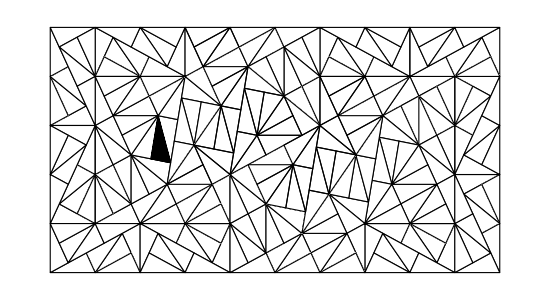

```mathematica
recursionlevel=3;
huemultiplier=0;
A=Graphics[{EdgeForm[{Thin,Black}],{Hue[Mod[N[Apply[ArcTan,huemultiplier{#[[2]]-#[[3]]+{.1,.1}}]],1]],Polygon[#]}&/@Flatten[Nest[Recurse/@Flatten[#,1]&,{initialshape},recursionlevel],1]},ImageSize-> {550,300}];
B=Graphics[{EdgeForm[{Thin,Black}],{Black,Polygon[Flatten[Nest[Recurse/@Flatten[#,1]&,{initialshape},recursionlevel],1][[157]]]}}];
pinwheel1=Show[A,B]
```

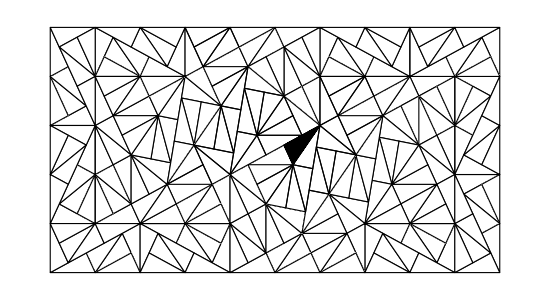

```mathematica
recursionlevel=3;
huemultiplier=0;
A=Graphics[{EdgeForm[{Thin,Black}],{Hue[Mod[N[Apply[ArcTan,huemultiplier{#[[2]]-#[[3]]+{.1,.1}}]],1]],Polygon[#]}&/@Flatten[Nest[Recurse/@Flatten[#,1]&,{initialshape},recursionlevel],1]},ImageSize-> {550,300}];
B=Graphics[{EdgeForm[{Thin,Black}],{Black,Polygon[Flatten[Nest[Recurse/@Flatten[#,1]&,{initialshape},recursionlevel],1][[70]]]}}];
pinwheel2=Show[A,B]
```

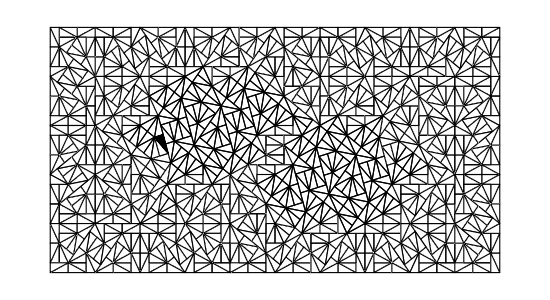

```mathematica
recursionlevel=4;
huemultiplier=0;
A=Graphics[{EdgeForm[{Thin,Black}],{Hue[Mod[N[Apply[ArcTan,huemultiplier{#[[2]]-#[[3]]+{.1,.1}}]],1]],Polygon[#]}&/@Flatten[Nest[Recurse/@Flatten[#,1]&,{initialshape},recursionlevel],1]},ImageSize-> {550,300}];
B=Graphics[{EdgeForm[{Thin,Black}],{Black,Polygon[Flatten[Nest[Recurse/@Flatten[#,1]&,{initialshape},recursionlevel],1][[783]]]}}];
pinwheel3=Show[A,B]
```

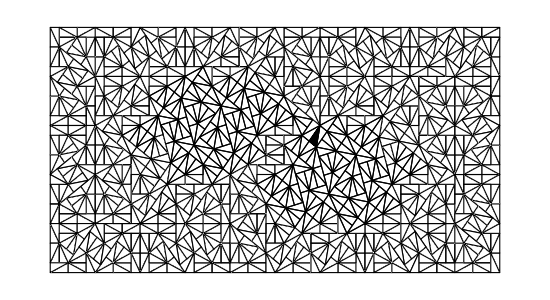

```mathematica
recursionlevel=4;
huemultiplier=0;
A=Graphics[{EdgeForm[{Thin,Black}],{Hue[Mod[N[Apply[ArcTan,huemultiplier{#[[2]]-#[[3]]+{.1,.1}}]],1]],Polygon[#]}&/@Flatten[Nest[Recurse/@Flatten[#,1]&,{initialshape},recursionlevel],1]},ImageSize-> {550,300}];
B=Graphics[{EdgeForm[{Thin,Black}],{Black,Polygon[Flatten[Nest[Recurse/@Flatten[#,1]&,{initialshape},recursionlevel],1][[300]]]}}];
pinwheel4=Show[A,B]
```

```mathematica
Export["pinwheel1.jpg",pinwheel1,ImageResolution->300]
Export["pinwheel2.jpg",pinwheel2,ImageResolution->300]
Export["pinwheel3.jpg",pinwheel3,ImageResolution->300]
Export["pinwheel4.jpg",pinwheel4,ImageResolution->300]
```

pinwheel1.jpg

pinwheel2.jpg

pinwheel3.jpg

pinwheel4.jpg